Here I want to find the area of a circle in the worst way possible
This approach is motivated by finding the delay distribution in a MCP pore
The sensible thing to do is to prove the approach with a circle then move on


given a unit circle
x=cos(ϕ)
y=sin(ϕ)

displace a circle up by w and find the arc length that remains in the original circle
integrate this arc length in order to find the circle area

```mathematica
xpos[p_]=Cos[p];
ypos[p_]=Sin[p];
wmax:=2*ypos[π/2];
```

```mathematica
intersectionpts=Solve[{xpos[a]==xpos[b], 
ypos[a]==ypos[b]+w},{a,b}]
```

Solve::ivar: 1.15435 is not a valid variable.

Solve[{Cos[a]==0.404516,Sin[a]==0.914531+w},{a,1.15435}]

```mathematica
Intersect11=intersectionpts[[2,1,2]]/.C[1]->0
Intersect12=intersectionpts[[1,1,2]]/.C[1]->0
Intersect21=intersectionpts[[2,2,2]]/.C[2]->0
Intersect22=intersectionpts[[1,2,2]]/.C[2]->0
```

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==0.914531+w},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve[{Cos[a]==0.404516,Sin[a]==0.914531+w},{a,1.15435}]⟦2,1,2⟧

0.404516

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==0.914531+w},{a,1.15435}]⟦2,2,2⟧ is longer than depth of object.

Solve[{Cos[a]==0.404516,Sin[a]==0.914531+w},{a,1.15435}]⟦2,2,2⟧

0.914531+w

```mathematica
ypos[(3 π)/2]
```

-1

## Area Under the region between intersections

The idea that the arc length is the right thing to relate some small segment of depths to the surface area at the detector surface is not strictly correct
instead it is better to think about what the change in 


Find the area between the x axis and the circle arc between intersection points
A=∫y(x)ⅆx 
do a change of var
x=cos(ϕ)
dx/dϕ=-sin(ϕ)
A=∫y(ϕ)(-sin(ϕ)) ⅆϕ

```mathematica
Manipulate[
Module[{wtmp,wtmp2},
wtmp=wfac*wmax;
wtmp2=0.01*wmax;
Show[
ParametricPlot[{xpos[a],ypos[a]},{a,-π,π},PlotLabel->StringForm["``.",wfac],
PlotRange->{{-1.5,1.5},{-1,1}*wmax}],
ParametricPlot[{xpos[a],ypos[a]+wtmp},{a,-π,π}],
ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w->wtmp,Intersect11/.w->wtmp},PlotStyle->{Red}],
ParametricPlot[{xpos[a],ypos[a]+wtmp},{a,Intersect21/.w->wtmp,Intersect22/.w->wtmp},PlotStyle->{Green}]
]],{wfac,10^-6,0.99999}
]
```

ParametricPlot::prng: Value of option PlotRange -> {{-1.5,1.5},{-wmax,wmax}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::prng: Value of option PlotRange -> {{-1.5,1.5},{-wmax,wmax}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ParametricPlot::plln: Limiting value Intersect12 in {a,Intersect12/.w→wtmp$188267,Intersect11/.w→wtmp$188267} is not a machine-sized real number.

ParametricPlot::plln: Limiting value Intersect21 in {a,Intersect21/.w→wtmp$188267,Intersect22/.w→wtmp$188267} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$188267,Intersect11/.w→wtmp$188267},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$188267},{a,Intersect21/.w→wtmp$188267,Intersect22/.w→wtmp$188267},PlotStyle→{Green}]].

ParametricPlot::plln: Limiting value Intersect12 in {a,Intersect12/.w→wtmp$188267,Intersect11/.w→wtmp$188267} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$188267,Intersect11/.w→wtmp$188267},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$188267},{a,Intersect21/.w→wtmp$188267,Intersect22/.w→wtmp$188267},PlotStyle→{Green}]].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==0.914531+w},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

General::stop: Further output of Solve::ivar will be suppressed during this calculation.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$189151,Intersect11/.w→wtmp$189151} is not a machine-sized real number.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,2,2⟧ in {a,Intersect21/.w→wtmp$189151,Intersect22/.w→wtmp$189151} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$189151,Intersect11/.w→wtmp$189151},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$189151},{a,Intersect21/.w→wtmp$189151,Intersect22/.w→wtmp$189151},PlotStyle→{Green}]].

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$189151,Intersect11/.w→wtmp$189151} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$189151,Intersect11/.w→wtmp$189151},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$189151},{a,Intersect21/.w→wtmp$189151,Intersect22/.w→wtmp$189151},PlotStyle→{Green}]].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==0.914531+w},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

General::stop: Further output of Solve::ivar will be suppressed during this calculation.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$220793,Intersect11/.w→wtmp$220793} is not a machine-sized real number.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,2,2⟧ in {a,Intersect21/.w→wtmp$220793,Intersect22/.w→wtmp$220793} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$220793,Intersect11/.w→wtmp$220793},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$220793},{a,Intersect21/.w→wtmp$220793,Intersect22/.w→wtmp$220793},PlotStyle→{Green}]].

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$220793,Intersect11/.w→wtmp$220793} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$220793,Intersect11/.w→wtmp$220793},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$220793},{a,Intersect21/.w→wtmp$220793,Intersect22/.w→wtmp$220793},PlotStyle→{Green}]].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==0.914531+w},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

General::stop: Further output of Solve::ivar will be suppressed during this calculation.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$256734,Intersect11/.w→wtmp$256734} is not a machine-sized real number.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,2,2⟧ in {a,Intersect21/.w→wtmp$256734,Intersect22/.w→wtmp$256734} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$256734,Intersect11/.w→wtmp$256734},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$256734},{a,Intersect21/.w→wtmp$256734,Intersect22/.w→wtmp$256734},PlotStyle→{Green}]].

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$256734,Intersect11/.w→wtmp$256734} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$256734,Intersect11/.w→wtmp$256734},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$256734},{a,Intersect21/.w→wtmp$256734,Intersect22/.w→wtmp$256734},PlotStyle→{Green}]].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==0.914531+w},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

General::stop: Further output of Solve::ivar will be suppressed during this calculation.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$258678,Intersect11/.w→wtmp$258678} is not a machine-sized real number.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,2,2⟧ in {a,Intersect21/.w→wtmp$258678,Intersect22/.w→wtmp$258678} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$258678,Intersect11/.w→wtmp$258678},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$258678},{a,Intersect21/.w→wtmp$258678,Intersect22/.w→wtmp$258678},PlotStyle→{Green}]].

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$258678,Intersect11/.w→wtmp$258678} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$258678,Intersect11/.w→wtmp$258678},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$258678},{a,Intersect21/.w→wtmp$258678,Intersect22/.w→wtmp$258678},PlotStyle→{Green}]].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==0.914531+w},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

General::stop: Further output of Solve::ivar will be suppressed during this calculation.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$269065,Intersect11/.w→wtmp$269065} is not a machine-sized real number.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,2,2⟧ in {a,Intersect21/.w→wtmp$269065,Intersect22/.w→wtmp$269065} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$269065,Intersect11/.w→wtmp$269065},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$269065},{a,Intersect21/.w→wtmp$269065,Intersect22/.w→wtmp$269065},PlotStyle→{Green}]].

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$269065,Intersect11/.w→wtmp$269065} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$269065,Intersect11/.w→wtmp$269065},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$269065},{a,Intersect21/.w→wtmp$269065,Intersect22/.w→wtmp$269065},PlotStyle→{Green}]].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==0.914531+w},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

General::stop: Further output of Solve::ivar will be suppressed during this calculation.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$269561,Intersect11/.w→wtmp$269561} is not a machine-sized real number.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,2,2⟧ in {a,Intersect21/.w→wtmp$269561,Intersect22/.w→wtmp$269561} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$269561,Intersect11/.w→wtmp$269561},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$269561},{a,Intersect21/.w→wtmp$269561,Intersect22/.w→wtmp$269561},PlotStyle→{Green}]].

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$269561,Intersect11/.w→wtmp$269561} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$269561,Intersect11/.w→wtmp$269561},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$269561},{a,Intersect21/.w→wtmp$269561,Intersect22/.w→wtmp$269561},PlotStyle→{Green}]].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==0.914531+w},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

General::stop: Further output of Solve::ivar will be suppressed during this calculation.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$271849,Intersect11/.w→wtmp$271849} is not a machine-sized real number.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,2,2⟧ in {a,Intersect21/.w→wtmp$271849,Intersect22/.w→wtmp$271849} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$271849,Intersect11/.w→wtmp$271849},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$271849},{a,Intersect21/.w→wtmp$271849,Intersect22/.w→wtmp$271849},PlotStyle→{Green}]].

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$271849,Intersect11/.w→wtmp$271849} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$271849,Intersect11/.w→wtmp$271849},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$271849},{a,Intersect21/.w→wtmp$271849,Intersect22/.w→wtmp$271849},PlotStyle→{Green}]].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==0.914531+w},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

General::stop: Further output of Solve::ivar will be suppressed during this calculation.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$274403,Intersect11/.w→wtmp$274403} is not a machine-sized real number.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,2,2⟧ in {a,Intersect21/.w→wtmp$274403,Intersect22/.w→wtmp$274403} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$274403,Intersect11/.w→wtmp$274403},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$274403},{a,Intersect21/.w→wtmp$274403,Intersect22/.w→wtmp$274403},PlotStyle→{Green}]].

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$274403,Intersect11/.w→wtmp$274403} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$274403,Intersect11/.w→wtmp$274403},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$274403},{a,Intersect21/.w→wtmp$274403,Intersect22/.w→wtmp$274403},PlotStyle→{Green}]].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==0.914531+w},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

General::stop: Further output of Solve::ivar will be suppressed during this calculation.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$276144,Intersect11/.w→wtmp$276144} is not a machine-sized real number.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,2,2⟧ in {a,Intersect21/.w→wtmp$276144,Intersect22/.w→wtmp$276144} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$276144,Intersect11/.w→wtmp$276144},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$276144},{a,Intersect21/.w→wtmp$276144,Intersect22/.w→wtmp$276144},PlotStyle→{Green}]].

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$276144,Intersect11/.w→wtmp$276144} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$276144,Intersect11/.w→wtmp$276144},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$276144},{a,Intersect21/.w→wtmp$276144,Intersect22/.w→wtmp$276144},PlotStyle→{Green}]].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==0.914531+w},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

General::stop: Further output of Solve::ivar will be suppressed during this calculation.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$310069,Intersect11/.w→wtmp$310069} is not a machine-sized real number.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,2,2⟧ in {a,Intersect21/.w→wtmp$310069,Intersect22/.w→wtmp$310069} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$310069,Intersect11/.w→wtmp$310069},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$310069},{a,Intersect21/.w→wtmp$310069,Intersect22/.w→wtmp$310069},PlotStyle→{Green}]].

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$310069,Intersect11/.w→wtmp$310069} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$310069,Intersect11/.w→wtmp$310069},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$310069},{a,Intersect21/.w→wtmp$310069,Intersect22/.w→wtmp$310069},PlotStyle→{Green}]].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==0.914531+w},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

General::stop: Further output of Solve::ivar will be suppressed during this calculation.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$312663,Intersect11/.w→wtmp$312663} is not a machine-sized real number.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,2,2⟧ in {a,Intersect21/.w→wtmp$312663,Intersect22/.w→wtmp$312663} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$312663,Intersect11/.w→wtmp$312663},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$312663},{a,Intersect21/.w→wtmp$312663,Intersect22/.w→wtmp$312663},PlotStyle→{Green}]].

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$312663,Intersect11/.w→wtmp$312663} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$312663,Intersect11/.w→wtmp$312663},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$312663},{a,Intersect21/.w→wtmp$312663,Intersect22/.w→wtmp$312663},PlotStyle→{Green}]].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==0.914531+w},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

General::stop: Further output of Solve::ivar will be suppressed during this calculation.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$314480,Intersect11/.w→wtmp$314480} is not a machine-sized real number.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,2,2⟧ in {a,Intersect21/.w→wtmp$314480,Intersect22/.w→wtmp$314480} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$314480,Intersect11/.w→wtmp$314480},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$314480},{a,Intersect21/.w→wtmp$314480,Intersect22/.w→wtmp$314480},PlotStyle→{Green}]].

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$314480,Intersect11/.w→wtmp$314480} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$314480,Intersect11/.w→wtmp$314480},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$314480},{a,Intersect21/.w→wtmp$314480,Intersect22/.w→wtmp$314480},PlotStyle→{Green}]].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==0.914531+w},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

General::stop: Further output of Solve::ivar will be suppressed during this calculation.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$331972,Intersect11/.w→wtmp$331972} is not a machine-sized real number.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,2,2⟧ in {a,Intersect21/.w→wtmp$331972,Intersect22/.w→wtmp$331972} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$331972,Intersect11/.w→wtmp$331972},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$331972},{a,Intersect21/.w→wtmp$331972,Intersect22/.w→wtmp$331972},PlotStyle→{Green}]].

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$331972,Intersect11/.w→wtmp$331972} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$331972,Intersect11/.w→wtmp$331972},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$331972},{a,Intersect21/.w→wtmp$331972,Intersect22/.w→wtmp$331972},PlotStyle→{Green}]].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==0.914531+w},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

General::stop: Further output of Solve::ivar will be suppressed during this calculation.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$333654,Intersect11/.w→wtmp$333654} is not a machine-sized real number.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,2,2⟧ in {a,Intersect21/.w→wtmp$333654,Intersect22/.w→wtmp$333654} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$333654,Intersect11/.w→wtmp$333654},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$333654},{a,Intersect21/.w→wtmp$333654,Intersect22/.w→wtmp$333654},PlotStyle→{Green}]].

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$333654,Intersect11/.w→wtmp$333654} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$333654,Intersect11/.w→wtmp$333654},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$333654},{a,Intersect21/.w→wtmp$333654,Intersect22/.w→wtmp$333654},PlotStyle→{Green}]].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==0.914531+w},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

General::stop: Further output of Solve::ivar will be suppressed during this calculation.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$335588,Intersect11/.w→wtmp$335588} is not a machine-sized real number.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,2,2⟧ in {a,Intersect21/.w→wtmp$335588,Intersect22/.w→wtmp$335588} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$335588,Intersect11/.w→wtmp$335588},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$335588},{a,Intersect21/.w→wtmp$335588,Intersect22/.w→wtmp$335588},PlotStyle→{Green}]].

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$335588,Intersect11/.w→wtmp$335588} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$335588,Intersect11/.w→wtmp$335588},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$335588},{a,Intersect21/.w→wtmp$335588,Intersect22/.w→wtmp$335588},PlotStyle→{Green}]].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==0.914531+w},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

General::stop: Further output of Solve::ivar will be suppressed during this calculation.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$339056,Intersect11/.w→wtmp$339056} is not a machine-sized real number.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,2,2⟧ in {a,Intersect21/.w→wtmp$339056,Intersect22/.w→wtmp$339056} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$339056,Intersect11/.w→wtmp$339056},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$339056},{a,Intersect21/.w→wtmp$339056,Intersect22/.w→wtmp$339056},PlotStyle→{Green}]].

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$339056,Intersect11/.w→wtmp$339056} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$339056,Intersect11/.w→wtmp$339056},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$339056},{a,Intersect21/.w→wtmp$339056,Intersect22/.w→wtmp$339056},PlotStyle→{Green}]].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==0.914531+w},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

General::stop: Further output of Solve::ivar will be suppressed during this calculation.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$340263,Intersect11/.w→wtmp$340263} is not a machine-sized real number.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,2,2⟧ in {a,Intersect21/.w→wtmp$340263,Intersect22/.w→wtmp$340263} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$340263,Intersect11/.w→wtmp$340263},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$340263},{a,Intersect21/.w→wtmp$340263,Intersect22/.w→wtmp$340263},PlotStyle→{Green}]].

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$340263,Intersect11/.w→wtmp$340263} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$340263,Intersect11/.w→wtmp$340263},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$340263},{a,Intersect21/.w→wtmp$340263,Intersect22/.w→wtmp$340263},PlotStyle→{Green}]].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==0.914531+w},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

General::stop: Further output of Solve::ivar will be suppressed during this calculation.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$344846,Intersect11/.w→wtmp$344846} is not a machine-sized real number.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,2,2⟧ in {a,Intersect21/.w→wtmp$344846,Intersect22/.w→wtmp$344846} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$344846,Intersect11/.w→wtmp$344846},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$344846},{a,Intersect21/.w→wtmp$344846,Intersect22/.w→wtmp$344846},PlotStyle→{Green}]].

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$344846,Intersect11/.w→wtmp$344846} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$344846,Intersect11/.w→wtmp$344846},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$344846},{a,Intersect21/.w→wtmp$344846,Intersect22/.w→wtmp$344846},PlotStyle→{Green}]].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==0.914531+w},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

General::stop: Further output of Solve::ivar will be suppressed during this calculation.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$346270,Intersect11/.w→wtmp$346270} is not a machine-sized real number.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,2,2⟧ in {a,Intersect21/.w→wtmp$346270,Intersect22/.w→wtmp$346270} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$346270,Intersect11/.w→wtmp$346270},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$346270},{a,Intersect21/.w→wtmp$346270,Intersect22/.w→wtmp$346270},PlotStyle→{Green}]].

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$346270,Intersect11/.w→wtmp$346270} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$346270,Intersect11/.w→wtmp$346270},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$346270},{a,Intersect21/.w→wtmp$346270,Intersect22/.w→wtmp$346270},PlotStyle→{Green}]].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==0.914531+w},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

General::stop: Further output of Solve::ivar will be suppressed during this calculation.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$347694,Intersect11/.w→wtmp$347694} is not a machine-sized real number.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,2,2⟧ in {a,Intersect21/.w→wtmp$347694,Intersect22/.w→wtmp$347694} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$347694,Intersect11/.w→wtmp$347694},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$347694},{a,Intersect21/.w→wtmp$347694,Intersect22/.w→wtmp$347694},PlotStyle→{Green}]].

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$347694,Intersect11/.w→wtmp$347694} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$347694,Intersect11/.w→wtmp$347694},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$347694},{a,Intersect21/.w→wtmp$347694,Intersect22/.w→wtmp$347694},PlotStyle→{Green}]].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==0.914531+w},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

General::stop: Further output of Solve::ivar will be suppressed during this calculation.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$349118,Intersect11/.w→wtmp$349118} is not a machine-sized real number.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,2,2⟧ in {a,Intersect21/.w→wtmp$349118,Intersect22/.w→wtmp$349118} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$349118,Intersect11/.w→wtmp$349118},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$349118},{a,Intersect21/.w→wtmp$349118,Intersect22/.w→wtmp$349118},PlotStyle→{Green}]].

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$349118,Intersect11/.w→wtmp$349118} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$349118,Intersect11/.w→wtmp$349118},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$349118},{a,Intersect21/.w→wtmp$349118,Intersect22/.w→wtmp$349118},PlotStyle→{Green}]].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==0.914531+w},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

General::stop: Further output of Solve::ivar will be suppressed during this calculation.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$350542,Intersect11/.w→wtmp$350542} is not a machine-sized real number.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,2,2⟧ in {a,Intersect21/.w→wtmp$350542,Intersect22/.w→wtmp$350542} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$350542,Intersect11/.w→wtmp$350542},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$350542},{a,Intersect21/.w→wtmp$350542,Intersect22/.w→wtmp$350542},PlotStyle→{Green}]].

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$350542,Intersect11/.w→wtmp$350542} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$350542,Intersect11/.w→wtmp$350542},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$350542},{a,Intersect21/.w→wtmp$350542,Intersect22/.w→wtmp$350542},PlotStyle→{Green}]].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==0.914531+w},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

General::stop: Further output of Solve::ivar will be suppressed during this calculation.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$351966,Intersect11/.w→wtmp$351966} is not a machine-sized real number.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,2,2⟧ in {a,Intersect21/.w→wtmp$351966,Intersect22/.w→wtmp$351966} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$351966,Intersect11/.w→wtmp$351966},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$351966},{a,Intersect21/.w→wtmp$351966,Intersect22/.w→wtmp$351966},PlotStyle→{Green}]].

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$351966,Intersect11/.w→wtmp$351966} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$351966,Intersect11/.w→wtmp$351966},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$351966},{a,Intersect21/.w→wtmp$351966,Intersect22/.w→wtmp$351966},PlotStyle→{Green}]].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==0.914531+w},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

General::stop: Further output of Solve::ivar will be suppressed during this calculation.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$395070,Intersect11/.w→wtmp$395070} is not a machine-sized real number.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,2,2⟧ in {a,Intersect21/.w→wtmp$395070,Intersect22/.w→wtmp$395070} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$395070,Intersect11/.w→wtmp$395070},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$395070},{a,Intersect21/.w→wtmp$395070,Intersect22/.w→wtmp$395070},PlotStyle→{Green}]].

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$395070,Intersect11/.w→wtmp$395070} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$395070,Intersect11/.w→wtmp$395070},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$395070},{a,Intersect21/.w→wtmp$395070,Intersect22/.w→wtmp$395070},PlotStyle→{Green}]].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==0.914531+w},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

General::stop: Further output of Solve::ivar will be suppressed during this calculation.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$403738,Intersect11/.w→wtmp$403738} is not a machine-sized real number.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,2,2⟧ in {a,Intersect21/.w→wtmp$403738,Intersect22/.w→wtmp$403738} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$403738,Intersect11/.w→wtmp$403738},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$403738},{a,Intersect21/.w→wtmp$403738,Intersect22/.w→wtmp$403738},PlotStyle→{Green}]].

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$403738,Intersect11/.w→wtmp$403738} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$403738,Intersect11/.w→wtmp$403738},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$403738},{a,Intersect21/.w→wtmp$403738,Intersect22/.w→wtmp$403738},PlotStyle→{Green}]].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==0.914531+w},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

General::stop: Further output of Solve::ivar will be suppressed during this calculation.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$412280,Intersect11/.w→wtmp$412280} is not a machine-sized real number.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,2,2⟧ in {a,Intersect21/.w→wtmp$412280,Intersect22/.w→wtmp$412280} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$412280,Intersect11/.w→wtmp$412280},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$412280},{a,Intersect21/.w→wtmp$412280,Intersect22/.w→wtmp$412280},PlotStyle→{Green}]].

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$412280,Intersect11/.w→wtmp$412280} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$412280,Intersect11/.w→wtmp$412280},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$412280},{a,Intersect21/.w→wtmp$412280,Intersect22/.w→wtmp$412280},PlotStyle→{Green}]].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==0.914531+w},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

General::stop: Further output of Solve::ivar will be suppressed during this calculation.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$420814,Intersect11/.w→wtmp$420814} is not a machine-sized real number.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,2,2⟧ in {a,Intersect21/.w→wtmp$420814,Intersect22/.w→wtmp$420814} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$420814,Intersect11/.w→wtmp$420814},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$420814},{a,Intersect21/.w→wtmp$420814,Intersect22/.w→wtmp$420814},PlotStyle→{Green}]].

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$420814,Intersect11/.w→wtmp$420814} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$420814,Intersect11/.w→wtmp$420814},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$420814},{a,Intersect21/.w→wtmp$420814,Intersect22/.w→wtmp$420814},PlotStyle→{Green}]].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==0.914531+w},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

General::stop: Further output of Solve::ivar will be suppressed during this calculation.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$467900,Intersect11/.w→wtmp$467900} is not a machine-sized real number.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,2,2⟧ in {a,Intersect21/.w→wtmp$467900,Intersect22/.w→wtmp$467900} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$467900,Intersect11/.w→wtmp$467900},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$467900},{a,Intersect21/.w→wtmp$467900,Intersect22/.w→wtmp$467900},PlotStyle→{Green}]].

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$467900,Intersect11/.w→wtmp$467900} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$467900,Intersect11/.w→wtmp$467900},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$467900},{a,Intersect21/.w→wtmp$467900,Intersect22/.w→wtmp$467900},PlotStyle→{Green}]].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==0.914531+w},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

General::stop: Further output of Solve::ivar will be suppressed during this calculation.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$476413,Intersect11/.w→wtmp$476413} is not a machine-sized real number.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,2,2⟧ in {a,Intersect21/.w→wtmp$476413,Intersect22/.w→wtmp$476413} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$476413,Intersect11/.w→wtmp$476413},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$476413},{a,Intersect21/.w→wtmp$476413,Intersect22/.w→wtmp$476413},PlotStyle→{Green}]].

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$476413,Intersect11/.w→wtmp$476413} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$476413,Intersect11/.w→wtmp$476413},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$476413},{a,Intersect21/.w→wtmp$476413,Intersect22/.w→wtmp$476413},PlotStyle→{Green}]].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==0.914531+w},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

General::stop: Further output of Solve::ivar will be suppressed during this calculation.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$484723,Intersect11/.w→wtmp$484723} is not a machine-sized real number.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,2,2⟧ in {a,Intersect21/.w→wtmp$484723,Intersect22/.w→wtmp$484723} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$484723,Intersect11/.w→wtmp$484723},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$484723},{a,Intersect21/.w→wtmp$484723,Intersect22/.w→wtmp$484723},PlotStyle→{Green}]].

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$484723,Intersect11/.w→wtmp$484723} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$484723,Intersect11/.w→wtmp$484723},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$484723},{a,Intersect21/.w→wtmp$484723,Intersect22/.w→wtmp$484723},PlotStyle→{Green}]].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==0.914531+w},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

General::stop: Further output of Solve::ivar will be suppressed during this calculation.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$493458,Intersect11/.w→wtmp$493458} is not a machine-sized real number.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,2,2⟧ in {a,Intersect21/.w→wtmp$493458,Intersect22/.w→wtmp$493458} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$493458,Intersect11/.w→wtmp$493458},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$493458},{a,Intersect21/.w→wtmp$493458,Intersect22/.w→wtmp$493458},PlotStyle→{Green}]].

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$493458,Intersect11/.w→wtmp$493458} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$493458,Intersect11/.w→wtmp$493458},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$493458},{a,Intersect21/.w→wtmp$493458,Intersect22/.w→wtmp$493458},PlotStyle→{Green}]].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==0.914531+w},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

General::stop: Further output of Solve::ivar will be suppressed during this calculation.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$499926,Intersect11/.w→wtmp$499926} is not a machine-sized real number.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,2,2⟧ in {a,Intersect21/.w→wtmp$499926,Intersect22/.w→wtmp$499926} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$499926,Intersect11/.w→wtmp$499926},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$499926},{a,Intersect21/.w→wtmp$499926,Intersect22/.w→wtmp$499926},PlotStyle→{Green}]].

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$499926,Intersect11/.w→wtmp$499926} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$499926,Intersect11/.w→wtmp$499926},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$499926},{a,Intersect21/.w→wtmp$499926,Intersect22/.w→wtmp$499926},PlotStyle→{Green}]].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==0.914531+w},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

General::stop: Further output of Solve::ivar will be suppressed during this calculation.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$514384,Intersect11/.w→wtmp$514384} is not a machine-sized real number.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,2,2⟧ in {a,Intersect21/.w→wtmp$514384,Intersect22/.w→wtmp$514384} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$514384,Intersect11/.w→wtmp$514384},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$514384},{a,Intersect21/.w→wtmp$514384,Intersect22/.w→wtmp$514384},PlotStyle→{Green}]].

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$514384,Intersect11/.w→wtmp$514384} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$514384,Intersect11/.w→wtmp$514384},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$514384},{a,Intersect21/.w→wtmp$514384,Intersect22/.w→wtmp$514384},PlotStyle→{Green}]].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==0.914531+w},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

General::stop: Further output of Solve::ivar will be suppressed during this calculation.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$518947,Intersect11/.w→wtmp$518947} is not a machine-sized real number.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,2,2⟧ in {a,Intersect21/.w→wtmp$518947,Intersect22/.w→wtmp$518947} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$518947,Intersect11/.w→wtmp$518947},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$518947},{a,Intersect21/.w→wtmp$518947,Intersect22/.w→wtmp$518947},PlotStyle→{Green}]].

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$518947,Intersect11/.w→wtmp$518947} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$518947,Intersect11/.w→wtmp$518947},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$518947},{a,Intersect21/.w→wtmp$518947,Intersect22/.w→wtmp$518947},PlotStyle→{Green}]].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==0.914531+w},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

General::stop: Further output of Solve::ivar will be suppressed during this calculation.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$520356,Intersect11/.w→wtmp$520356} is not a machine-sized real number.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,2,2⟧ in {a,Intersect21/.w→wtmp$520356,Intersect22/.w→wtmp$520356} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$520356,Intersect11/.w→wtmp$520356},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$520356},{a,Intersect21/.w→wtmp$520356,Intersect22/.w→wtmp$520356},PlotStyle→{Green}]].

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$520356,Intersect11/.w→wtmp$520356} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$520356,Intersect11/.w→wtmp$520356},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$520356},{a,Intersect21/.w→wtmp$520356,Intersect22/.w→wtmp$520356},PlotStyle→{Green}]].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==0.914531+w},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

General::stop: Further output of Solve::ivar will be suppressed during this calculation.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$547772,Intersect11/.w→wtmp$547772} is not a machine-sized real number.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,2,2⟧ in {a,Intersect21/.w→wtmp$547772,Intersect22/.w→wtmp$547772} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$547772,Intersect11/.w→wtmp$547772},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$547772},{a,Intersect21/.w→wtmp$547772,Intersect22/.w→wtmp$547772},PlotStyle→{Green}]].

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$547772,Intersect11/.w→wtmp$547772} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$547772,Intersect11/.w→wtmp$547772},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$547772},{a,Intersect21/.w→wtmp$547772,Intersect22/.w→wtmp$547772},PlotStyle→{Green}]].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==0.914531+w},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

General::stop: Further output of Solve::ivar will be suppressed during this calculation.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$549255,Intersect11/.w→wtmp$549255} is not a machine-sized real number.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,2,2⟧ in {a,Intersect21/.w→wtmp$549255,Intersect22/.w→wtmp$549255} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$549255,Intersect11/.w→wtmp$549255},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$549255},{a,Intersect21/.w→wtmp$549255,Intersect22/.w→wtmp$549255},PlotStyle→{Green}]].

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$549255,Intersect11/.w→wtmp$549255} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$549255,Intersect11/.w→wtmp$549255},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$549255},{a,Intersect21/.w→wtmp$549255,Intersect22/.w→wtmp$549255},PlotStyle→{Green}]].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==0.914531+w},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

General::stop: Further output of Solve::ivar will be suppressed during this calculation.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$550137,Intersect11/.w→wtmp$550137} is not a machine-sized real number.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,2,2⟧ in {a,Intersect21/.w→wtmp$550137,Intersect22/.w→wtmp$550137} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$550137,Intersect11/.w→wtmp$550137},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$550137},{a,Intersect21/.w→wtmp$550137,Intersect22/.w→wtmp$550137},PlotStyle→{Green}]].

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$550137,Intersect11/.w→wtmp$550137} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$550137,Intersect11/.w→wtmp$550137},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$550137},{a,Intersect21/.w→wtmp$550137,Intersect22/.w→wtmp$550137},PlotStyle→{Green}]].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==0.914531+w},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

General::stop: Further output of Solve::ivar will be suppressed during this calculation.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$552163,Intersect11/.w→wtmp$552163} is not a machine-sized real number.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,2,2⟧ in {a,Intersect21/.w→wtmp$552163,Intersect22/.w→wtmp$552163} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$552163,Intersect11/.w→wtmp$552163},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$552163},{a,Intersect21/.w→wtmp$552163,Intersect22/.w→wtmp$552163},PlotStyle→{Green}]].

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$552163,Intersect11/.w→wtmp$552163} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$552163,Intersect11/.w→wtmp$552163},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$552163},{a,Intersect21/.w→wtmp$552163,Intersect22/.w→wtmp$552163},PlotStyle→{Green}]].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==0.914531+w},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

General::stop: Further output of Solve::ivar will be suppressed during this calculation.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$554536,Intersect11/.w→wtmp$554536} is not a machine-sized real number.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,2,2⟧ in {a,Intersect21/.w→wtmp$554536,Intersect22/.w→wtmp$554536} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$554536,Intersect11/.w→wtmp$554536},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$554536},{a,Intersect21/.w→wtmp$554536,Intersect22/.w→wtmp$554536},PlotStyle→{Green}]].

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$554536,Intersect11/.w→wtmp$554536} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$554536,Intersect11/.w→wtmp$554536},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$554536},{a,Intersect21/.w→wtmp$554536,Intersect22/.w→wtmp$554536},PlotStyle→{Green}]].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==0.914531+w},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

General::stop: Further output of Solve::ivar will be suppressed during this calculation.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$556233,Intersect11/.w→wtmp$556233} is not a machine-sized real number.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,2,2⟧ in {a,Intersect21/.w→wtmp$556233,Intersect22/.w→wtmp$556233} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$556233,Intersect11/.w→wtmp$556233},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$556233},{a,Intersect21/.w→wtmp$556233,Intersect22/.w→wtmp$556233},PlotStyle→{Green}]].

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$556233,Intersect11/.w→wtmp$556233} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$556233,Intersect11/.w→wtmp$556233},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$556233},{a,Intersect21/.w→wtmp$556233,Intersect22/.w→wtmp$556233},PlotStyle→{Green}]].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==0.914531+w},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

Solve::ivar: 1.15435 is not a valid variable.

General::stop: Further output of Solve::ivar will be suppressed during this calculation.

Part::partd: Part specification Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$558190,Intersect11/.w→wtmp$558190} is not a machine-sized real number.

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,2,2⟧ in {a,Intersect21/.w→wtmp$558190,Intersect22/.w→wtmp$558190} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$558190,Intersect11/.w→wtmp$558190},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$558190},{a,Intersect21/.w→wtmp$558190,Intersect22/.w→wtmp$558190},PlotStyle→{Green}]].

ParametricPlot::plln: Limiting value Solve[{Cos[a]==0.404516,Sin[a]==1.53853},{a,1.15435}]⟦2,1,2⟧ in {a,Intersect12/.w→wtmp$558190,Intersect11/.w→wtmp$558190} is not a machine-sized real number.

General::stop: Further output of ParametricPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,,ParametricPlot[{xpos[a],ypos[a]},{a,Intersect12/.w→wtmp$558190,Intersect11/.w→wtmp$558190},PlotStyle→{Red}],ParametricPlot[{xpos[a],ypos[a]+wtmp$558190},{a,Intersect21/.w→wtmp$558190,Intersect22/.w→wtmp$558190},PlotStyle→{Green}]].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

π+1/4 (-w √(4-w^2)-(-2+4 w) ArcTan[-√(4-w^2),-w]-(2-4 w) ArcTan[√(4-w^2),-w])+1/4 (-w √(4-w^2)-2 ArcTan[-√(4-w^2),w]+2 ArcTan[√(4-w^2),w])

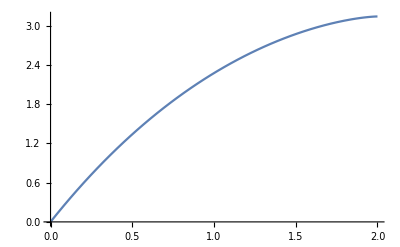

```mathematica
areaArc=π-Integrate[(w+ypos[ϕ] * D[xpos[ϕ],ϕ])  ,{ϕ,Intersect21,Intersect22}]-Integrate[ypos[ϕ] * D[xpos[ϕ],ϕ]  ,{ϕ,Intersect12,Intersect11}]
Plot[areaArc,{w,0,wmax}]
```

```mathematica
dareaArc=FullSimplify[D[areaArc,w],Assumptions->{w∈Reals,w>0}]
```

((-2+w) w)/(√(4-w^2))-ArcTan[-√(4-w^2),-w]+ArcTan[√(4-w^2),-w]

```mathematica
dareaArc/.w->0.5
```

dareaArc

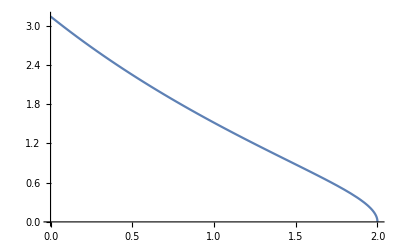

```mathematica
Plot[dareaArc,{w,0,wmax}]
```

```mathematica
Integrate[Abs[dareaArc],{w,0,wmax}]
```

π

```mathematica
N[(ArcTan[-√(4-w^2),-w]+ArcTan[√(4-w^2),-w]+π)/.w->1.5]
```

0.

## Arc length (old)

```mathematica
ArcLenIndef=Integrate[√((D[xpos[ϕ],ϕ])^2+(D[ypos[ϕ],ϕ])^2),ϕ]
ArcLenDefManual=(ArcLenIndef/.ϕ->Intersect1)-(ArcLenIndef/.ϕ->Intersect2)
```

ϕ

-ArcTan[-1/2 √(4-w^2),-w/2]+ArcTan[(√(4-w^2))/2,-w/2]

```mathematica
FullSimplify[(ArcLenDefManual/.w->0)*wmax]
```

-2 π

```mathematica
NIntegrate[ArcLenDefManual,{w,0,wmax},AccuracyGoal->10,PrecisionGoal->10,WorkingPrecision->10]
```

4.

```mathematica
Manipulate[
Module[{wtmp,wtmp2},
wtmp=wfac*wmax;
wtmp2=0.01*wmax;
Show[
ParametricPlot[{xpos[a],ypos[a]},{a,-π,π},PlotLabel->StringForm["``.,``.",wfac,N[Re[ArcLenDefManual/.w->wtmp],2]],
PlotRange->{{-1.5,1.5},{-1,1}*wmax}],
ParametricPlot[{xpos[a],ypos[a]+wtmp},{a,-π,π}],
ParametricPlot[{xpos[a],ypos[a]+wtmp},{a,Intersect1/.w->wtmp,Intersect2/.w->wtmp},PlotStyle->{Red}],
ParametricPlot[{xpos[a],ypos[a]+wtmp+wtmp2},{a,Intersect1/.w->wtmp,Intersect2/.w->wtmp},PlotStyle->{Red}]
]],{wfac,10^-6,0.99999}
]
```

```mathematica
ListPlot[{{xpos[Intersect1],zpos[Intersect1]+d},{xpos[Intersect2],zpos[Intersect2]+d}}/.{α->alphaTemp,d->b},PlotStyle->Red,PlotMarkers->{Automatic, Medium}],
PlotRange->{{-1.1,1.1},zmax[alphaTemp]*{-0.7,0.8}}
```